```mathematica
Exit
```

```mathematica
p=0.31 2;
size=96p;
λ=0.810;
padRatio=3;
```

```mathematica
rotL[data_]:=RotateLeft[data, Floor@Dimensions[data][[#]]/2&/@Range[Length@Dimensions[data]]];
(* corner at orign to center at origin *)
rotR[data_]:=RotateRight[data, Floor@Dimensions[data][[#]]/2&/@Range[Length@Dimensions[data]]];
(* {x,y} means {x,y}/λ, {kx,ky} means {kx,ky}/k *)
FFT[f_] :=rotR[Fourier[f, FourierParameters->{1, -1}]];
iFFT[f_]:=InverseFourier[rotL[f], FourierParameters->{1, -1}];

centerRange[n_,d_]:=Table[(i-n/2-.5)*d,{i,n}];
```

```mathematica
k0=2π/λ
{nx,ny}={Floor[size/p],Floor[size/p]};
{lx,ly}={nx*p,ny*p};
{dx,dy}={p,p};
{dkx, dky}={(2π)/(p*nx),(2π)/(p*ny)};
{padx,pady}= {(padRatio-1)/2 nx,(padRatio-1)/2 ny};
{x,y}={centerRange[nx,dx],centerRange[ny,dy]};
Echo[{nx p,ny p},"Sample size in um: "];
Echo[{nx,ny},"Sample size in pixel: "];
```

7.75702

Sample size in um:   {59.52,59.52}

Sample size in pixel:   {96,96}

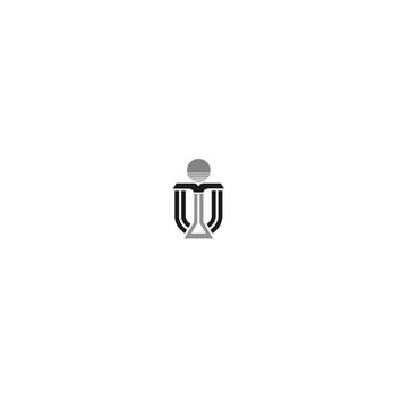

```mathematica
SetDirectory[NotebookDirectory[]];
img = Import["/home/stnav/Projects/jensen-lab-mathematica/hologram/hkust.png"];
target =img//ImageResize[#,{ny,nx}]&//ColorConvert[#, "Grayscale"]&//ImageData//#/Max[#]&//(1-#)&//ArrayPad[#,{pady, padx}]&;
target//ArrayPlot
```

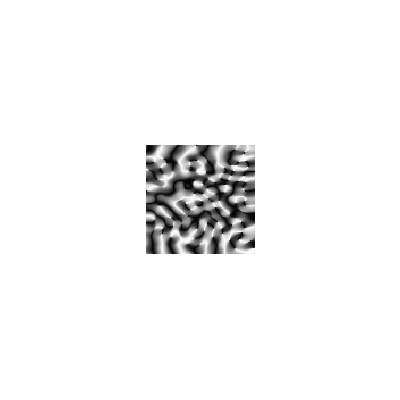
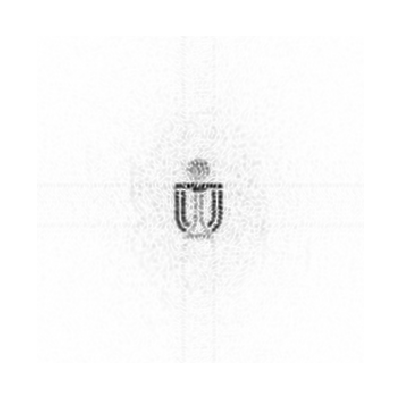

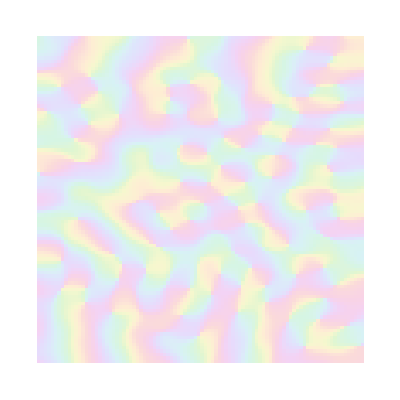

```mathematica
gsLoop = 100;
source = ConstantArray[1,{ny,nx}]//ArrayPad[#, {pady, padx}]&;
loopA = source*Exp[ⅈ RandomReal[{0,2π},source//Dimensions]];

For[i = 0, i < gsLoop,i = i + 1,
loopB = Abs[source] * Exp[ⅈ*Arg[loopA]];
loopC = FFT[loopB];
loopD = Abs[target] * Exp[ⅈ*Arg[loopC]];
loopA = iFFT[loopD];
]
Enear = source * Exp[ⅈ* Arg[loopA]];
Efar = FFT[Enear];
{ArrayPlot[Arg[Enear]],ArrayPlot[Abs[Efar]]}
meta = Enear[[pady+1;;-pady-1, padx+1;;-padx-1]];
meta//ComplexArrayPlot
```

```mathematica
fname ="hologram_hkustLogo_wl810_fnone_gsLoop100iter_";
Export[StringJoin[fname, "Abs", ".csv"], Abs[meta]];
Export[StringJoin[fname, "Arg", ".csv"], Arg[meta]];
Export[StringJoin[fname, "Mask", ".csv"], ConstantArray[1,Dimensions[meta]]];
```

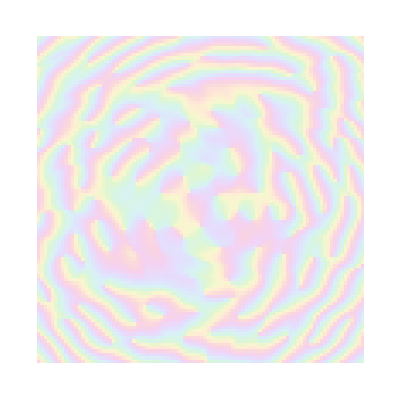
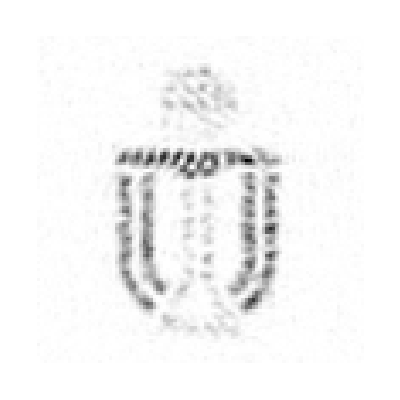

```mathematica
f = 150;
metaFocus = meta*Exp[-ⅈ k0(√(Outer[Plus,y^2,x^2]+f^2)- f)];
H[A_,z_,{dx_,dy_}] := Module[{nx, ny, kx, ky},
	{nx, ny}=Dimensions[A][[#]]&/@{2,1};
	{kx,ky}=centerRange@@#&/@{{nx, (2π)/(dx nx)},{ny,(2π)/(dy ny)}};
	Exp[I *z*Sqrt[k0^2 - Outer[Plus,ky^2,kx^2]]]
]; 
forwardPropagate[A_,z_,{dx_, dy_}]:=iFFT[FFT[A] *H[A,z,{dx, dy}]];
farFieldFocus=forwardPropagate[metaFocus,f, {p, p}]//Abs[#]^2&;
{metaFocus//ComplexArrayPlot,farFieldFocus//ArrayPlot}
```

```mathematica
fname ="hologram_hkustLogo_wl810_f150um_gsLoop100iter_";
Export[StringJoin[fname, "Abs", ".csv"], Abs[metaFocus]];
Export[StringJoin[fname, "Arg", ".csv"], Arg[metaFocus]];
Export[StringJoin[fname, "Mask", ".csv"], ConstantArray[1,Dimensions[metaFocus]]];
```

General::munfl: Exp[-1794.35+0. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1781.03+0. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1767.74+0. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

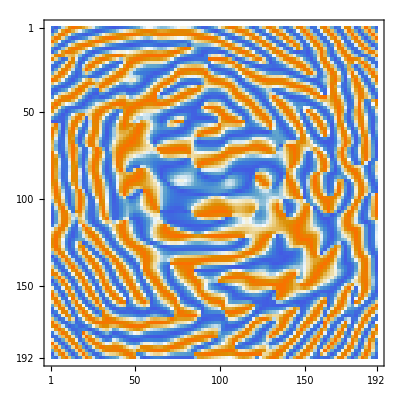
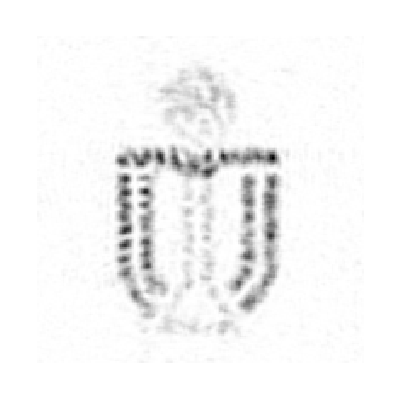

```mathematica
abs =Import["holoPairAbs.csv"];
arg = Import["holoPairArg.csv"];
metaPair = abs*Exp[ⅈ*arg];
farFieldPair = forwardPropagate[metaPair, f, {p/2,p/2}]//Abs[#]^2&;
{metaPair//MatrixPlot, farFieldPair//ArrayPlot}
```